```mathematica
(*Jungeun Kim, Department of Physics, KAIST - 2024.11.26.*)
```

```mathematica
Ff[t_]:=-(0.9 - Cos[ 2 Pi t])/(1 -0.9 Cos[2 Pi t])^3
```

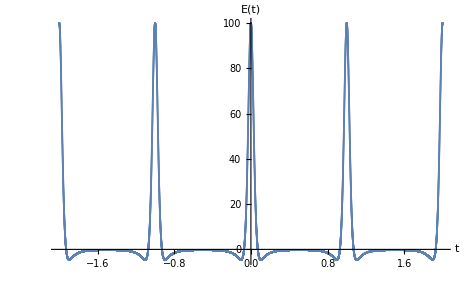

```mathematica
Dom=Table[i,{i,-2,2,0.0001}]//Quiet;
Ran=ParallelTable[Ff[i],{i,-2,2,0.0001}]//Quiet;
data = Transpose@{Dom, Ran}
ListPlot[data, PlotRange->All, AxesLabel->{Style["t",Bold,16],Style["E(t)",Bold,16]}]
```

```mathematica
Dom2=Table[i,{i,-0.5,0.5,0.0001}]//Quiet;
Ran2=ParallelTable[Ff[i],{i,-0.5,0.5,0.0001}]//Quiet;
(*FourierTransform[(0.9 - Cos[2 Pi t])/(1 -0.9 Cos[2 Pi t])^3,t,ω, Assumptions->ω>0] *)
Fourier[Ran2]
```

$Aborted

```mathematica
FourierTransform[(0.9 - Cos[2 Pi t])/(1 -0.9 Cos[2 Pi t])^3,t,ω]
```